# Dynamic Axion Evolution

### Dependencies and Globals

```mathematica
Quit[]
```

```mathematica
(* LOAD PACKAGES *)
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,xcolor}"}];

(* PRECISION AND ACCURACY *)
NPRECISON = 13;

(* GLOBALS *)
Msun=1.989*10^30;(* kg *)
GN = 6.67*10^-11; (* SI *)
G=(*6.70883*10^(-57)*)1; (* eV^-2 *)
clight = 2.99792458*10^8; (* m/s *)
eV2joules=1.60218*10^(-19);
GeV2joules=1.60218*10^(-10);
mN = 0.939563; (* GeV *)
hbarGeV=6.582119569*10^(-25); (* GeV S *)
hbarJ = 1.05457*10^(-34); (* J s *)
hbarGeo = hbarJ * (GN / clight^4) * clight; (* m^2 *)
(*GNeV = 6.70883*10^(-39);*)
σN = 0.059;(* GeV *)(* eV*s *)
rkm=10^3 / (hbarGeV*clight);
rm=1/(hbarGeV*clight);
mpi = 0.134977;
fpi = 0.130;
mu = 0.0017;
md = 0.0041;
RSTART=10^-8;
RHOFRAC=10^-12;

MeVperfm3 2 Jperm3=(10^-3*GeV2joules) * (10^(-15))^(-3);
Jperm3 2 m2 = GN / clight^4;
GeV2m = GeV2joules*GN/clight^4;

RescaleMRPair km Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]]/10^3, ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRΛTriplet km Msun dim0[MRΛTriplet_,scales_]:={(MRΛTriplet[[1]])*scales[[1]]/10^3, ((MRΛTriplet[[2]])*scales[[3]]*clight^2/GN)/Msun,MRΛTriplet[[3]]}
RescaleMRPair m Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRPair m kg[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]]*clight^2/GN)*scales[[1]]^3 * scales[[2]])}
RescaleM kg[mass_,scales_]:=((mass*clight^2/GN)*scales[[1]]^3 * scales[[2]])
RescaleR m[radius_,scales_]:=(radius)*scales[[1]]

TOV replacements={λ'[r]->D[Log[1/(1 - 2*M[r]/r)],r],λ''[r]->D[-Exp[λ[r]]*(2*M[r]/r^2 - 8*Pi*r*ρ[r]),r],
Exp[λ[r]]->1/(1 - 2*M[r]/r),
Exp[-λ[r]]->(1 - 2*M[r]/r),
λ[r]->Log[1/(1 - 2*M[r]/r)],Derivative[1][p][r]->-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),
Derivative[2][p][r]->Simplify[D[-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),r]],
Derivative[1][ν][r]->-2*(Derivative[1][p][r])/(p[r]+ρ[r]),
M'[r]->4*Pi*r^2*ρ[r]};

c1=RGBColor[101/255,144/255,255/255];
c2=RGBColor[121/255,94/255,240/255];
c3=RGBColor[221/255,38/255,129/255];
c4=RGBColor[255/255,97/255,2/255];
c5=RGBColor[254/255,176/255,1/255];
c6=RGBColor[200/255,200/255,200/255];
```

```mathematica
mpi^2*fpi^2*GeV2m^4/hbarGeo^3
```

5.30159×10^-11

### Functions

```mathematica
(* SOLVE FOR MASS FUNCTION, DENSITY FUNCTION, MASS, AND RADIUS GIVEN EQUATION OF STATE AND CENTRAL DENSITY *)
GetGenericMassRadius[ρcentral_,EOS_,dEOSdrhoofr_,ρfrac_,scales_]:=Module[{dMdr,dPdr,ρc=ρcentral,sols,Rstar,Mstar,mass,density,rstart=RSTART,rend=50.0,alpha,Acoef,density out,density total,ddensitydr,mass out,mass total,EOSscaled,dEOSscaleddrhoofr,M,ρ,rt,ν,ν total,ν out,νsols,r},
(*EOSscaled[ρ_]:=EOS[ρ*scales[[2]]]/scales[[4]];*)
(*dEOSdrhoofr[ρ_]:= D[EOS[ρ],ρ];*)
dMdr=D[M[rt],rt]==4*Pi*rt^2*ρ[rt]*(scales[[1]]^3* scales[[2]]/scales[[3]]);
dPdr=D[ρ[rt],rt]==-((dEOSdrhoofr[scales[[2]]*ρ[rt]])^(-1))*(M[rt]+4*Pi*rt^3*EOS[ρ[rt]*scales[[2]]]*scales[[1]]^3/scales[[3]])*(EOS[ρ[rt]*scales[[2]]]/scales[[2]]+ρ[rt])/(rt*(rt*scales[[1]]/scales[[3]]-2*M[rt]));
sols=NDSolve[{{dMdr,dPdr},{M[rstart]==(4/3)*Pi*ρc*rstart^3*scales[[2]]*scales[[1]]^3/scales[[3]],ρ[rstart]==ρc(*-(2*Pi/3)*(ρc+EOS[ρc*scales[[2]]]/scales[[2]])*(ρc*scales[[2]]+3*EOS[ρc*scales[[2]]])*rstart^2*scales[[1]]^2*),WhenEvent[ρ[rt]==ρc*ρfrac,{Rstar=rt,Mstar=M[rt]};"StopIntegration"]}},{M,ρ},{rt,rstart,rend},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
mass[rt_]:=Evaluate[M[rt]/.sols];
density[rt_]:=Evaluate[ρ[rt]/.sols];
ddensitydr[rt_]:=Evaluate[D[density[rt],rt]];
νsols = NDSolve[{D[ν[rt],rt]/scales[[1]]==2*(mass[rt]*scales[[3]]+4*Pi*rt^3*scales[[1]]^3*EOS[density[rt]*scales[[2]]])/(rt*scales[[1]]*(rt*scales[[1]]-2*mass[rt]*scales[[3]])),ν[Rstar]==1 - 2*Mstar*scales[[3]]/(Rstar*scales[[1]])},{ν},{rt,rstart,rend},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
ν[r_]:=Evaluate[ν[r]/.νsols];
alpha=-(ddensitydr[Rstar]/density[Rstar]);
Acoef=density[Rstar];
density out[rt_]:=Acoef*Exp[-alpha*(rt - Rstar)];
density total[rt_]:=If[rt<=Rstar,density[rt],density out[rt]];
mass out[rt_]:=Mstar -((Acoef*(-1+Exp[alpha*(-rt+Rstar)]))/alpha);
mass total[rt_]:=If[rt<=Rstar,mass[rt],mass out[rt]];
ν out[rt]:=1 - 2*Mstar/rt;
ν total[rt_]:=If[rt<=Rstar,ν[rt],ν out[rt]];
{{Rstar,Mstar},{mass total,density total,ν,density}}]

(* SOLVE FOR DYNAMIC AXION AND AXION DERIVATIVE FIELDS *)
(*GetDynamicAxionField[massradiussol_,mass_,density_,ν_,ma_,fa_,scales_,initialprofile_]:=Module[{density coefficient sub,dθpdr rscaled,dθdr rscaled,mythetaTfncsols,NSradiusscaled,r,rt,tt,θsol,θprimesol,rstart=10.0/10^5,NSradius=massradiussol[[1]],θsolin,θsolout,θprimesolin,θprimesolout,d2θdr2 rscaled},
d2θdr2 rscaled = Exp[-ν[r]]* D[θT[rt,tt],tt,tt]-(1 - 2*mass[rt]*scales[[3]]/(rt*scales[[1]]))* D[θTp[rt,tt],rt]==-(ma^2*scales[[1]]^2/hbarGeo^2)* (1 - density[rt]*scales[[2]]*hbarGeo^3*σN/(4*fa^2*ma^2*mN))*Sin[θT[rt,tt]]*(Cos[θT[rt,tt]]/Abs[Cos[θT[rt,tt]]]);
θTpeqn = D[θT[rt,tt],rt]==θTp[rt,tt];
mythetaTfncsols=NDSolve[{d2θdr2 rscaled,θT[NSradius,0.0]==2*Pi*Exp[-ma*scales[[1]]*NSradius/hbarGeo],θTp[NSradius,0.0]==-2*Pi*Exp[-ma*scales[[1]]*NSradius/hbarGeo]*(1/NSradius + scales[[1]]*ma/hbarGeo),θT[rstart,0.0]==2*Pi*Exp[-ma*scales[[1]]*rstart/hbarGeo]},{θT, θTp},{rt,rstart,NSradius},PrecisionGoal->NPRECISON,AccuracyGoal->NPRECISON][[1]];
θsolin[rt_]:=Evaluate[θT[rt]/.mythetaTfncsols];
θprimesolin[rt_]:=Evaluate[θTp[rt]/.mythetaTfncsols];
θsolout[rt_]:=(2*Pi*NSradius/rt)*Exp[-ma*scales[[1]]*rt/hbarGeo];
θprimesolout[rt_]:=(-2*Pi*NSradius/rt)*(Exp[-ma*scales[[1]]*rt/hbarGeo]/rt+ (scales[[1]]*ma/hbarGeo)*Exp[-ma*scales[[1]]*rt/hbarGeo]);
θsol[rt_]:=If[rt<NSradius,θsolin[rt],θsolout[rt]];
θprimesol[rt_]:=If[rt<NSradius,θprimesolin[rt],θprimesolout[rt]];
{{θsol,θprimesol}}]*)
```

### Solve example pde 2

#### solve for NS background

```mathematica
ϵ=(*0.4*)10^-1;
fasub=10^16;
mafasubs = {Sqrt[fpi^2*mpi^2*ϵ/(2*fasub^2)],fasub}*GeV2m;
```

```mathematica
FILEBASE="eos_nb0.05_G0.02_nb_0.27_G_0.06";
EOSPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/input_stable_eos_files_p_of_nb_fixed/";
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/EOS-MR/output_stable_eos_files_p_of_nb_fixed/";
EOSData=Import[StringJoin[EOSPATH,FILEBASE,".csv"],"CSV"];
(*EOSData=Import[StringJoin[EOSPATH,"eos.dat"]];*)
MRData=Import[StringJoin[MRPATH,FILEBASE,"_observables.dat"](*,"CSV"*)];
EOSDataLimited=EOSData[[1;;-1;;4,8;;9]];
centraldensities = EOSData[[1;;-1;;6,2]]*(MeVperfm3 2 Jperm3*Jperm3 2 m2);
(*EOSDataLimited=EOSData[[All,{3,2}]];*)
MRDataLimited=MRData[[1;;Dimensions[MRData][[1]],{2,3}]];
MΛDataLimited=MRData[[1;;Dimensions[MRData][[1]],{3,5}]];
pressureEOS=ResourceFunction["CubicMonotonicInterpolation"][EOSDataLimited]; (* rho and p are in MeV / fm^3, so we need to rescale *) 
(* I actually shouldn't need to rescale. That should just be wrapped up in whatever I choose as my ρscale variable in the TOV solver. *)
dpressureEOS[ρ_]:=Evaluate[D[pressureEOS[ρ],ρ]];
maxdensity=Max[EOSDataLimited[[1;;-1,1]]];
mindensity=Min[EOSDataLimited[[1;;-1,1]]];
pressureEOS m2[rhobar_]:=pressureEOS[rhobar/(MeVperfm3 2 Jperm3*Jperm3 2 m2)]*(MeVperfm3 2 Jperm3*Jperm3 2 m2)
dpressureEOS m2[ρ_]:=Evaluate[D[pressureEOS m2[ρ],ρ]];
domainscaled={mindensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2),maxdensity*(MeVperfm3 2 Jperm3*Jperm3 2 m2)};
MRfnc=ResourceFunction["CubicMonotonicInterpolation"][MRDataLimited];
```

```mathematica
myscales={10^5,10^-10,1};
mrmρ vals = Quiet[GetGenericMassRadius[4.0,pressureEOS m2,dpressureEOS m2,RHOFRAC,myscales]];
```

```mathematica
massfnc[r_]:=Evaluate[mrmρ vals[[2]][[1]][r]];
densityfnc[r_]:=Evaluate[mrmρ vals[[2]][[2]][r]];
nufnc[r_]:=Evaluate[mrmρ vals[[2]][[3]][r]];
densityin[r_]:=Evaluate[mrmρ vals[[2]][[4]][r]];
pressurefnc[r_]:=pressureEOS m2[densityfnc[r]*myscales[[2]]];
```

```mathematica
densitynormvals=Table[{r*myscales[[1]]/10^3,densityfnc[r] / densityfnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityvals=Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
densityderivativevals=Table[{r*myscales[[1]]/10^3,Derivative[1][densityfnc][r]*myscales[[2]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/10000}]//Quiet;
pressurenormvals=Table[{r*myscales[[1]]/10^3,pressurefnc[r] / pressurefnc[0.01*mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
pressurevals=Table[{r*myscales[[1]]/10^3,pressurefnc[r]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
massnormvals=Table[{r*myscales[[1]]/10^3,massfnc[r]/massfnc[mrmρ vals[[1]][[1]]]},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
expansionparametervals = Table[{r*myscales[[1]]/10^3,densityfnc[r]*myscales[[2]]*hbarGeo^3*σN/(2*mafasubs[[1]]^2*mafasubs[[2]]^2*mN)},{r,0.01*mrmρ vals[[1]][[1]],1.2*mrmρ vals[[1]][[1]],mrmρ vals[[1]][[1]]/1000}]//Quiet;
```

#### Solve for axion field

```mathematica
(*θeqn =Exp[-nufnc[rt]]*-(1-(2*massfnc[rt]*myscales[[3]])/(rt*myscales[[1]]))*Derivative[1][θTp][rt] + (2*(massfnc[rt]*myscales[[3]]+2*Pi*rt^3*myscales[[1]]^3*(densityfnc[rt]*myscales[[2]]-pressurefnc[rt])-rt*myscales[[1]])/(rt^2*myscales[[1]]))*θTp[rt]==(mafasubs[[1]]^2*myscales[[1]]^2/hbarGeo^2)* ((1/2)- densityfnc[rt]*myscales[[2]]*hbarGeo^3*σN/(4*mafasubs[[1]]^2*mafasubs[[1]]^2*mN))*Sin[θT[rt]]*(Cos[θT[rt]]/Abs[Cos[θT[rt]]]);*)
```

```mathematica
Clear[solve,eqnset,un,t,x,parm,a,tmax,wp,x0,cons]
```

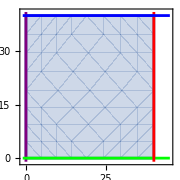

```mathematica
parm={a=40,tmax=40,wp=10,x0=0,cons=True};
boundaries={-t,-x,t-tmax,x-a};
Ω=ImplicitRegion[And@@(#≤0&/@boundaries),{t,x}];
Show[RegionPlot[Ω],ContourPlot[Evaluate[Thread[boundaries==0]],{t,-1,tmax+5},{x,-1,a+1},ContourStyle->{Purple,Green,Red,Blue,Purple}],PlotRange->{{-1,tmax+5},{-1,a+1}},AspectRatio->Automatic,ImageSize->Small]
```

```mathematica
eqnset={D[un[t,x],{t,2}]-D[un[t,x],{x,2}]+0.3*D[un[t,x],{t,1}]==-(-1.0(*+HeavisideTheta[x - a/4]*))*Sin[un[t,x]]*Cos[un[t,x]]/RealAbs[Cos[un[t,x]]]+NeumannValue[0,t==0],DirichletCondition[un[t,x]==2*Exp[-(x-a/8)^2/2]-2*Exp[-a^2/2],t==0]};
solv=Quiet[NDSolveValue[eqnset,un,{t,0,tmax},{x,0,a},Method->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.1}},InterpolationOrder->All,AccuracyGoal->3,PrecisionGoal->3]]
```

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

FindRoot::dfmin: The minimal damping factor of 1/10000 has been reached.

NDSolveValue::fempsf: PDESolve could not find a solution.

General::munfl: Exp[-800.] is too small to represent as a normalized machine number; precision may be lost.

FindRoot::dfmin: The minimal damping factor of 1/10000 has been reached.

NDSolveValue::fempsf: PDESolve could not find a solution.

NDSolveValue[{-un^(0,2)[t,x]+0.3 un^(1,0)[t,x]+un^(2,0)[t,x]==NeumannValue[0,t==0]+(1. Cos[un[t,x]] Sin[un[t,x]])/RealAbs[Cos[un[t,x]]],DirichletCondition[un[t,x]==-2/ⅇ^800+2 ⅇ^(-1/2 (-5+x)^2),t==0]},un,{t,0,40},{x,0,40},Method→{FiniteElement,MeshOptions→{MaxCellMeasure→0.1}},InterpolationOrder→All,AccuracyGoal→3,PrecisionGoal→3]

```mathematica
solv[3,4]
```

0.280366

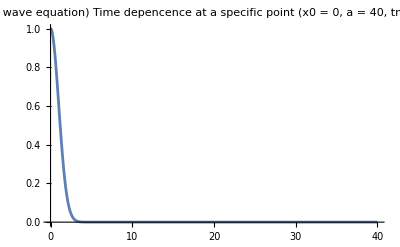

```mathematica
(*plot time dependence*)
Plot[solv[t,x0],{t,0,tmax},PlotRange->All,PlotLabel->"Numerical solution of a time dependent PDE (1D wave equation)\nTime depencence at a specific point\n (x0 = "<>ToString[x0]<>", a = "<>ToString[a]<>", tmax = "<>ToString[tmax]<>",\nWorkingPrecision = "<>ToString[wp]<>", consistency = "<>ToString[cons]<>")\n"]
```

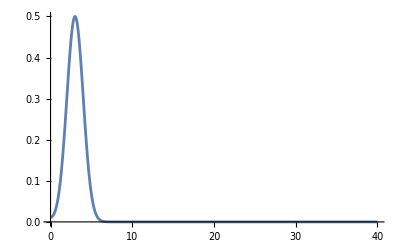

```mathematica
(*plot spatial dependence*)
t0=3;
Plot[solv[t0,x],{x,0,a},PlotRange->All,PerformanceGoal->"Quality"]
```

```mathematica
(* plot both spatial and time *)
```

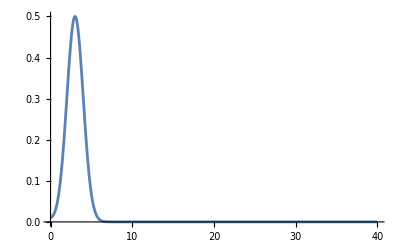

```mathematica
Plot[solv[3,x],{x,-a,a},PlotRange->All]
```

```mathematica
(* amplitude of the external BC should be set by the amount of axion inside, so this set of initial conditions doesn't really make sense either. *)
```

```mathematica
Manipulate[Plot[solv[t,x],{x,0,a},PlotRange->{{0,a},{-5,5}}],{t,0,30}]
```

My domain is a rectangle with boundaries at t = 0, t = t_final, r = 0, and r = r_exterior. To specify Neumann boundary conditions, we need to specify the value of the derivative at one half of the boundary along with a profile at the time boundary. I might also need to specify the second derivative at the time boundary. No because this is fixed by the specification of the initial profile.

This might actually be working.

### Solve Dynamic Axion

```mathematica
sol=NDSolve[{D[m[r,t],t,t]==1*10^-1*(D[m[r,t],r,r]-2/r*D[m[r,t],r]),m[r,0]==0.5*r,Derivative[0,1][m][r,0]==0.1(*,m[r,0.02]==0.5*)},m,{t,0,5},{r,0.9,1}]

f[r_,t_]:=(m/. sol[[1,1]])[r,t];

Plot3D[f[r,t],{t,0,5},{r,0.01,1},PlotRange->Full]
```

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable r. Artificial boundary effects may be present in the solution.

{{m→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {0.0100708,0.0003575} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
0.2+0.3 Exp[-1*0.01]
```

0.497015

```mathematica
0.5 - 0.0003575
```

0.499643